# Airy Disc

MH, v1 .0, 2021 _ 03 _ 09

## Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
```

## 2D

```mathematica
f[x_,y_]:=BesselJ[1,2π Sqrt[x^2+y^2]]^2/(π(x^2+y^2))
```

```mathematica
Plot3D[f[x,y],{x,-1,1},{y,-1,1},PlotRange->All]
```

-Graphics3D-

### Export

```mathematica
airyDisc2D=Plot3D[
f[x,y],{x,-1,1},{y,-1,1},
PlotRange->All,
LabelStyle->Directive[10,FontFamily->"Times New Roman"],
AxesLabel->{
Style["x",Italic,16,FontFamily->"Times New Roman"],
Style["y",Italic,16,FontFamily->"Times New Roman"],
Style["f(x,y)",Italic,16,FontFamily->"Times New Roman"]
},
Boxed->False,
PlotPoints->50,
MaxRecursion->5
]
```

-Graphics3D-

```mathematica
Export["airyDisc2D.png",airyDisc2D,ImageResolution->300];
```

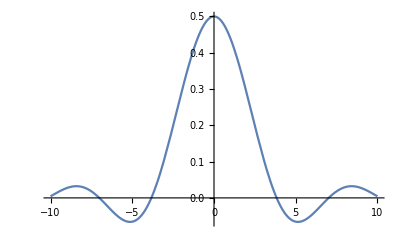

```mathematica
Plot[BesselJ[1,x]/x,{x,-10,10}]
```

## 3D

```mathematica
f[x_,y_,z_,α_]:=Integrate[BesselJ[0,α ρ Sqrt[x^2+y^2]]ρ,{ρ,0,1}]
```